# Chapter. AC voltammetry

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter7”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter7”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
(*Off[General::"spell"];
Off[General::"spell1"];*)
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->112,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12],Cell[TextData[{"AC voltammetry"}], FontFamily->"Arial",FontSize->12],None}, {None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Analytical solution","Finite difference methods","Analysis of data in the frequency domain","Square wave ac voltammetry","Summary","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily-> "Arial", 10, Plain],
Frame->True,
FrameLabel->None,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]}
];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial", 10, Plain],
Frame->True,
FrameLabel->None,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
Joined->True,
PlotStyle->{Black,AbsoluteThickness[.5]},
PlotLabel->None];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
(* options for ac voltammograms *)

optionA={
(*PlotRange:>{{0,n},{Min[data2]-0.1,Max[data2]+0.1}},*)
FrameTicks:>{ticks1[0,20000,5000,5],ticks1[.2,-1.2,-.2,5],ticks2[0,20000,5000,5],ticks2[.2,-1.2,-.2,5]},
RotateLabel->False,
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameLabel->{Style["increment",FontFamily->"Arial" ,10],Style["χ",FontFamily-> "Times New Roman" ,10, Plain],None,None},
ImagePadding->{{Inherited,5},{Inherited,Inherited}}
};
```

```mathematica
(* options for ac voltammograms *)

optionB={
PlotStyle-> {Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[-10,10,5,5],ticks1[2.,-2.,-.2,5],ticks2[-10,10,5,5],ticks2[2.,-2.,-.2,5]},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],Style["χ",FontFamily-> "Times New Roman",10],None,None}
};
```

```mathematica
(* options for ac voltammograms *)

optionBB={
PlotStyle-> {Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[-10,10,5,5],ticks1[.1,-.1,-.01,5],ticks2[-10,10,5,5],ticks2[.1,-.1,-.01,5]},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],Style["χ",FontFamily-> "Times New Roman",10],None,None}
};
```

```mathematica
(* options for ac voltammograms *)

optionB2={
PlotStyle-> {Black,AbsoluteThickness[0.5]},
FrameTicks:>{xTicks1,Automatic,xTicks3,Automatic},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],Style["χ",FontFamily-> "Times New Roman",10],None,None}
};
```

```mathematica
(* options for power spectrum plots *)

optionMain={
PlotStyle->{Black,AbsoluteThickness[0.5]},
PlotRange-> {{1,22},{0,3}},
FrameTicks:>{ticks1[0,50,5,5],ticks1[0,10,2,5],ticks2[0,50,5,5],ticks2[0,10,2,5]},FrameLabel->{"Frequency / π",None,None,None},
ImagePadding->{{Inherited,5},{Inherited,Inherited}}
};
```

```mathematica
(* options for insets in power spectrum plots *)

optionInset={
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[10,15,1,5],ticks1[0,1,.1,5],ticks2[10,15,1,5],ticks2[0,1,.2,5]},
PlotRange->{{9.8,14.8},{0,0.12}},
BaseStyle->{FontSize->9},
FrameLabel->{"Frequency / π",None,None,None},
ImagePadding->{{Inherited,3},{Inherited,Inherited}},
Joined->True
};
```

```mathematica
(* options for power spectrum plots *)

optionMain2={
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[0,50,5,5],ticks1[0,50,10,5],ticks2[0,50,5,5],ticks2[0,50,10,5]},
FrameLabel->{"Frequency / π",None,None,None},
ImagePadding->{{Inherited,5},{Inherited,Inherited}}
};
```

```mathematica
(* options for power spectrum plots *)

optionMain3={
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[0,500,50,5],ticks1[0,20,5,5],ticks2[0,500,50,5],ticks2[0,20,5,5]},
FrameLabel->{"Frequency / π",None,None,None}
};
```

```mathematica
(* options for square wave voltammograms *)
optionD={
FrameTicks:>{ticks1[-10,10,5,5],ticks1[-1,1,.5,5],ticks2[-10,10,5,5],ticks2[-1,1,.5,5]},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10,Italic],Style["χ",FontFamily-> "Times New Roman",10, "Plain"],None,None},
PlotRange:>{{10,-10},{Min[squareDiff⟦All,2⟧]-.1,Max[squareBack⟦All,2⟧]+.1}},
Epilog:> {Text["χ_b",{0,Max[squareBack⟦All,2⟧]-.1}],Text["χ_f",{0,Min[squareFor⟦All,2⟧]+.1}],Text["Δχ",{0,Min[squareDiff⟦All,2⟧]+.1}]}
};
```

```mathematica
(* options for dc voltammograms *)

dcOptions={Joined-> True,
(*PlotRange:> {{lowerLimit,upperLimit},{Min[newdata4]-0.03,Max[newdata4]+0.03}},*)
PlotStyle->{Black,AbsoluteThickness[.5]},
FrameTicks-> Automatic,
FrameLabel-> {Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",12,Italic],Style["√πχ",FontFamily-> "Times New Roman",12,Plain],None,None}};
```

```mathematica
(* options for square wave voltammograms *)

optionG={
FrameTicks:>{Automatic,yTicks2,Automatic,yTicks4},
PlotStyle->{Black,AbsoluteThickness[0.5]},
RotateLabel->False,
FrameLabel->{"increment","χ",None,None}};
```

```mathematica
ClearAll[𝒻,F,R,T,𝒟,α];
F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T = 298.; (*Absolute temperature*)
𝒻=F/(R*T);
𝒟=1.*10^-5;(*diffusion coefficient of substrate in cm^2 s^-1*)
α=0.5; (*transfer coefficient*)
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In ac voltammetric experiment a periodic signal is superimposed upon a dc potential sweep. Typically the periodic signal is either a sine wave or a square wave. In this chapter the numerical and analytical methods used to solve and simulate cyclic voltammograms are extended to ac methods beginning with sine wave ac and then square wave voltammetry. The fast Fourier transform can be applied to simulations of ac voltammograms to isolate particular harmonics, and in the case of square wave simulations, particular components.

## Chapter.Section Analytical solution

In the typical application of ac sine wave voltammetry a small amplitude sine wave is superimposed upon a slow dc potential sweep. Because the time domain of the dc component is long relative to the ac perturbation the analytical derivation of the response assumes that the dc component is effectively constant. Analytically we’ll consider only the reversible case but in §7.3 we’ll consider numerical solutions for the more general quasi-reversible case.
Under conditions of reversible electron transfer the equation describing the variation of current with potential was derived in Chapter 5. For the reaction

O + e ⇌ R

The concentration of O at the electrode surface is

c_O(0,t)=c_O^*-1/(n F (A(π D_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

If R is assumed to be initially absent from solution the concentration of R at the electrode surface is

c_R(0,t)=1/(n F (A(π D_R))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

Under reversible conditions the ratio of O to R at the electrode surface at any potential is given by the Nernst equation.

(c_O(0,t))/(c_R(0,t))=exp((n F)/(R T)(E(t)-E°'))
=ξexp((n F)/(R T)ΔEsin(ω t))

with

ξ=exp((n F)/(R T)(E_dc-E°'))

ω is the angular frequency of the ac voltage of peak amplitude Δ E, and E_dc is the dc voltage, that changes linearly according to

E_dc=E_i-υt

E_i is the initial potential and υ the sweep rate. Substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives

g(t)=1/(n F A (c_O^*(π D_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

with

g( t)=1/(γξexp((n F/R T)Δ E sin(ω t))+1)

with γ=(D_O/D_R)^(1/2). Because the dc potential is approximated to be constant, i.e. ξ is constant, during the course of an ac period the response can be broken into a constant dc component and a time varying ac component. Next step is to apply a Taylor series expansion (see Appendix 1) to the ac component of the exponential term about the point sinωt=0.

g( t)=∑_(p=0)^∞ d^(p)/(d t^(p))(1/(γξexp[(n F/R T)Δ E sin(ω t)]+1))_(sinωt=0)(sin^p ωt)/(p!)

To simplify the Mathematica expressions let f equal nFΔE/RT. Expanding up to the fourth term gives

```mathematica
ClearAll[ξ,f,ω,t,γ,g,gSeries];

g[t_]:=1/(1+γ*ξ*Exp[f*Sin[ω t]])

gSeries=Simplify[Series[g[t],{Sin[ω t],0,4}]]//Normal
```

1/(1+γ ξ)-(f γ ξ Sin[t ω])/(1+γ ξ)^2+(f^2 γ ξ (-1+γ ξ) Sin[t ω]^2)/(2 (1+γ ξ)^3)-(f^3 γ ξ (1-4 γ ξ+γ^2 ξ^2) Sin[t ω]^3)/(6 (1+γ ξ)^4)+(f^4 γ ξ (-1+11 γ ξ-11 γ^2 ξ^2+γ^3 ξ^3) Sin[t ω]^4)/(24 (1+γ ξ)^5)

Therefore g(t) can be represented as

g( t)=∑_(p=0)^∞ g_p(t)

where the subscript p indicates the harmonic number. If the ac amplitude is sufficiently small then contributions to each harmonic from higher order terms can be ignored and the dimensionless currents for the pth harmonic can be determined by solving eqn (Chapter.EquationNumbered)

g_p(t)=1/(n F A (c_O^*(π D_O))^(1/2))∫_0^t (i_p(τ))/(t-τ)^(1/2)ⅆτ

where g_p(t) is the pth term of the series expansion in eqn (Chapter.EquationNumbered). Taking the first term of the series expansion and substituting into eqn (Chapter.EquationNumbered) gives the Volterra equation for the zeroth harmonic or dc current.

1/(1+γξ)=1/(n F A (c_O^*(π D_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

Equation (Chapter.EquationNumbered), which was solved in the previous chapter, is a Volterra equation of the first kind with the general solution

(i(t))/(n F A (c_O^*(π D_O))^(1/2))=-2/π((t-τ)^(1/2)((dg(t))/dt))_0^t+2/π∫_0^t (t-τ)^(1/2)d/dτ((dg(t))/dt)_(t=τ)ⅆτ

For the first harmonic the dimensionless current is obtained from the second term in the series expansion of g(t).

g_1(t)=-(n F Δ E)/(R T)γξ/(1+γξ)^2 sin(ω t)=1/(n F A (c_O^*(π D_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

By changing the integration variable from τ to τ=z/ω eqn (Chapter.EquationNumbered) is rewritten as

φ(ω t)=-2/π((ω t-z)^(1/2)((dg_1(t))/dz))_0^(ω t)+2/π∫_0^(ω t) (ω t-z)^(1/2)d/dz((dg_1(t))/dz)_(ω t=z)ⅆz

with φ(ω t) given by

φ(ω t)=(i(ω t))/(n F A (c_O^*(πω D_O))^(1/2))

Remembering that for the ac response ξ is assumed to be time independent, the result is

φ_1(t)=-2/π((ω t-z)^(1/2)((dg_1(t))/dz))_0^(ω t)-2/π(n F Δ E)/(R T)γξ/(1+γξ)^2∫_0^t (ω t-z)^(1/2)d/dz((dsin(z))/dz)_(ω t=z)ⅆτ

Evaluating the first part on the right hand side of eqn (Chapter.EquationNumbered) gives

```mathematica
ClearAll[z,firstRHS,partA];

firstRHS[z_]:=(√(ωt-z))*(D[Evaluate[gSeries⟦2⟧/.ω*t-> ωt],ωt]/.ωt->z);partA=-2/π*(firstRHS[ωt]-firstRHS[0])//Simplify
```

-(2 f γ ξ √ωt)/(π (1+γ ξ)^2)

Evaluating the integral gives a result that is a function of Fresnel integrals (see functions.wolfram.com).

```mathematica
D[Sin[z],{z,2}]
```

-Sin[z]

```mathematica
ClearAll[z,partB];

partB=Assuming[f>0&&γ>0&&ξ>0&&ω>0&&Re[ωt]>0&&Im[ωt]==0,
 -2/π*(f γ ξ)/(1+γ ξ)^2*∫_0^ωt -Sin[z]*(√(ωt-z))ⅆz]
```

-(2 f γ ξ (-√ωt+√(π/2) (Cos[ωt] FresnelC[√(2/π) √ωt]+FresnelS[√(2/π) √ωt] Sin[ωt])))/(π (1+γ ξ)^2)

Both FresnelC[z] and FresnelS[z] approach 1/2 for large values of z. We can substitute 1/2 for each of the Fresnel integrals in the output above with a replacement rule. Setting the Fresnel integrals to 1/2 is analogous to the steady state assumption made by Smith in his derivation (see Further Reading). The Fresnel integrals allow us to estimate the errors inherent in this assumption. For example at t=20 the error is approximately one percent for a frequency of 50 Hz. After making this substitution partB reduces to

```mathematica
partB=partB/.{_FresnelC->1/2,_FresnelS->1/2}//FullSimplify
```

(f γ ξ (4 √ωt-√(2 π) (Cos[ωt]+Sin[ωt])))/(2 π (1+γ ξ)^2)

```mathematica
partA+partB//Simplify
```

-(f γ ξ (Cos[ωt]+Sin[ωt]))/(√(2 π) (1+γ ξ)^2)

Therefore

φ_1(t)=-(n F Δ E)/(R T)γξ/(1+γξ)^2(1/(2π))^(1/2)(cos(ωt)+sin(ω t))

The exponential terms can be converted to trigonometric terms using ExpToTrig, to conform with the customary representation of ac formulas. Substituting

```mathematica
ExpToTrig[Exp[j]/(1+Exp[j])^2]//Simplify
```

1/4 Sech[j/2]^2

1/(4cosh^2(j/2))=(exp(j))/(1+exp(j))^2

with j=(nF/RT)(E_dc-E°')+lnγ, into eqn (Chapter.EquationNumbered) gives the equation for the dimensionless first harmonic current

φ_1(t)=-(n F)/(R T)ΔE/(4cosh^2(j/2))(1/(2π))^(1/2)(cos(ωt)+sin(ω t))

We can make use of the relationship

A sin(nωt)+B cos(nωt)=(A^2+B^2)^(1/2)sin(nωt+cot^-1(A/B))

to further simplify eqn (Chapter.EquationNumbered). In this case A=B therefore eqn (Chapter.EquationNumbered) can be rearranged to

φ_1(t)=-(n F)/(R T)ΔE/(4 π^(1/2)cosh^2(j/2))sin(ω t+π/4)

Therefore the dimensionless ac current for the first harmonic can be written as

π^(1/2)χ_1(t)=((R T)/(n F))(i(ω t))/(n F A c_O^*Δ (E(ω D_O))^(1/2))=-1/(4cosh^2(j/2))sin(ω t+π/4)

so that the current for a reversible reaction will be 45 degrees out of phase with the voltage.
For the second harmonic, once again ignoring the contribution from higher order terms, g_2(t) is

g_2(t)=((n F Δ E)/(R T))^2(γ ξ (γ ξ-1))/(2(1+γξ)^3)sin^2(ωt)

The sin^2(ωt) term can be eliminated by making use of the relationship

sin^2(ωt)=1/2 (1-cos(2ωt))

Substituting this into eqn (Chapter.EquationNumbered) gives the equation that must be solved to produce the equation for the second harmonic the dimensionless current, χ_2(t).

∫_0^t (χ_2(τ))/(t-τ)^(1/2)ⅆτ=g_2(t)=((n F Δ E)/(R T))^2(γ ξ (γ ξ-1))/(4(1+γξ)^3)(1-cos(2ω t))

φ_2(t)=-(2/π[(ω t-z)^(1/2)((dg_1(t))/dz)])_0^(ω t)+2/π((n F Δ E)/(R T))^2(γ ξ (γ ξ-1))/(4(1+γξ)^3)∫_0^t (ω t-z)^(1/2)d/dz((d (1-cos(2ω t)))/dz)_(ω t=z)ⅆτ

The result is

```mathematica
ClearAll[z,firstRHS,partA,partB2];

firstRHS[z_]:=(√(ωt-z))*(D[Evaluate[gSeries⟦2⟧/.ω*t-> ωt],ωt]/.ωt->z);partA=-2/π*(firstRHS[ωt]-firstRHS[0])//Simplify
```

-(2 f γ ξ √ωt)/(π (1+γ ξ)^2)

```mathematica
partB2=Assuming[f>0&&γ>0&&ξ>0&&ω>0&&Re[ωt]>0&&Im[ωt]==0, 2/π*∫_0^ωt (D[Evaluate[TrigReduce[gSeries⟦3⟧/.ω*t-> ωt]],{ωt,2}]/.ωt-> z)*√(ωt-z)ⅆz]
```

(f^2 γ ξ (-1+γ ξ) (-Cos[2 ωt] FresnelS[(2 √ωt)/(√π)]+FresnelC[(2 √ωt)/(√π)] Sin[2 ωt]))/(2 √π (1+γ ξ)^3)

After again making the substitutions FresnelC[z] → 1/2 and FresnelS[z] → 1/2 the result reduces to

```mathematica
partB2=partB2/.{_FresnelC->1/2,_FresnelS->1/2}//FullSimplify
```

(f^2 γ ξ (-1+γ ξ) (-Cos[2 ωt]+Sin[2 ωt]))/(4 √π (1+γ ξ)^3)

Therefore the equation for the second harmonic is

χ_2(t)=((n F Δ E)/(R T))^2(γ ξ (γ ξ-1))/(4 π^(1/2) (1+γ ξ)^3)(cos(2ω t)-sin(2ω t))

Converting the exponential terms to trigonometric functions:

```mathematica
ExpToTrig[(Exp[j]*(Exp[j]-1))/(1+Exp[j])^3]//Simplify
```

2 Csch[j]^3 Sinh[j/2]^4

Different versions of Mathematica may yield different output. TrigFactorList can decompose these expressions to list of expressions and powers:

```mathematica
ClearAll[tmp];
tmp=TrigFactorList[ 2 Csch[j]^3 Sinh[j/2]^4]
```

{{4,-1},{Sinh[j/2],1},{Cosh[j/2],-3}}

Converting the list back into an expression gives:

```mathematica
Times@@(Power@@@tmp)
```

1/4 Sech[j/2]^2 Tanh[j/2]

sinh/cosh automatically gets converted to tanh. This can be prevented by applying HoldForm to the sinh and cosh expression. MapAt maps HoldForm to the positions in tmp where sinh and cosh are located.

```mathematica
Times@@(Power@@@MapAt[HoldForm,tmp,{{2,1},{3,1}}])
```

Sinh[j/2]/(4 Cosh[j/2]^3)

Substituting into (Chapter.EquationNumbered) gives

χ_2(t)=((n F Δ E)/(R T))^2(sinh(j/2))/(16 π^(1/2)cosh^3(j/2))(cos(2ω t)-sin(2ω t))

Using the relationship in eqn (Chapter.EquationNumbered) we have

χ_2(t)=((n F Δ E)/(R T))^2(sinh(j/2))/(16cosh^3(j/2))((2ω)/π)^(1/2)sin(2ωt-π/4)

To evaluate the contribution from higher order terms to each harmonic the terms sin^p(ωt) in eqn (Chapter.EquationNumbered) need to be reduced to some function of sin(nωt) and cos(nωt) where n is a positive integer. We can do this with the relationship

sin^n(x)={(-1)^n/2^n∑_(j=0)^n (-1)^j(n
j)sin[(n-2j)x] | for  n=2N+1
(-1)^n/2^n∑_(j=0)^n (-1)^j(n
j)cos[(n-2j)x] | for  n=2N

Mathematica is able to reduce powers of sine and cosine functions with the function TrigReduce. For example:

```mathematica
TrigReduce[Sin[x]^4]
```

1/8 (3-4 Cos[2 x]+Cos[4 x])

TrigReduce can be applied to the Taylor series expansion, for example:

```mathematica
ClearAll[ξ,f,ω,t,γ,g,tmp,gSeries2];

g[t_]:=1/(1+γ*ξ*Exp[f*Sin[ω*t]])

(* complex expression were not output in previous versions. We keep only reals *)

tmp=TrigReduce@Normal[Series[g[t],{Sin[ω*t],0,3}]];
gSeries2=Simplify[DeleteCases[#,_Complex,∞]& /@ tmp]
```

1/(24 (1+γ ξ)^4)(24+72 γ ξ-6 f^2 γ ξ+72 γ^2 ξ^2+24 γ^3 ξ^3+6 f^2 γ^3 ξ^3+48 f γ ξ ((1+γ ξ)^2+f^2 (1+γ ξ+γ^2 ξ^2)) Cos[t ω]-6 f^2 γ ξ (-1+γ^2 ξ^2) Cos[2 t ω]+48 f^3 γ ξ Cos[3 t ω]+48 f^3 γ^2 ξ^2 Cos[3 t ω]+48 f^3 γ^3 ξ^3 Cos[3 t ω]-24 f γ ξ Sin[t ω]-3 f^3 γ ξ Sin[t ω]-48 f γ^2 ξ^2 Sin[t ω]+12 f^3 γ^2 ξ^2 Sin[t ω]-24 f γ^3 ξ^3 Sin[t ω]-3 f^3 γ^3 ξ^3 Sin[t ω]+48 f^2 γ ξ Sin[2 t ω]+96 f^2 γ^2 ξ^2 Sin[2 t ω]+48 f^2 γ^3 ξ^3 Sin[2 t ω]+f^3 γ ξ Sin[3 t ω]-4 f^3 γ^2 ξ^2 Sin[3 t ω]+f^3 γ^3 ξ^3 Sin[3 t ω])

The individual harmonics can be extracted using the function Cases. Cases extracts a pattern from an expression. If we try to extract the individual harmonics the following expression doesn’t work:

```mathematica
Cases[gSeries2,_ Sin[t ω]]
```

{}

The placeholder in _Sin[t ω] tells Mathematica to search for all cases containing sin(ωt). If we add the option to search at all levels of the output above we get an answer but not what we expect.

```mathematica
Cases[gSeries2,_ Sin[t ω],∞]
```

{-24 f γ ξ Sin[t ω],-3 f^3 γ ξ Sin[t ω],-48 f γ^2 ξ^2 Sin[t ω],12 f^3 γ^2 ξ^2 Sin[t ω],-24 f γ^3 ξ^3 Sin[t ω],-3 f^3 γ^3 ξ^3 Sin[t ω]}

The reason this doesn’t work is that the expression gSeries2 is split into three subsections. If the expression could not be divided into subexpression applying AtomQ to the expression would yield True.

```mathematica
AtomQ[gSeries2]
```

False

In this case gSeries2 is composed of three subexpressions:

```mathematica
Length[gSeries2]
```

3

```mathematica
gSeries2⟦1⟧
gSeries2⟦2⟧
gSeries2⟦3⟧
```

1/24

1/(1+γ ξ)^4

24+72 γ ξ-6 f^2 γ ξ+72 γ^2 ξ^2+24 γ^3 ξ^3+6 f^2 γ^3 ξ^3+48 f γ ξ ((1+γ ξ)^2+f^2 (1+γ ξ+γ^2 ξ^2)) Cos[t ω]-6 f^2 γ ξ (-1+γ^2 ξ^2) Cos[2 t ω]+48 f^3 γ ξ Cos[3 t ω]+48 f^3 γ^2 ξ^2 Cos[3 t ω]+48 f^3 γ^3 ξ^3 Cos[3 t ω]-24 f γ ξ Sin[t ω]-3 f^3 γ ξ Sin[t ω]-48 f γ^2 ξ^2 Sin[t ω]+12 f^3 γ^2 ξ^2 Sin[t ω]-24 f γ^3 ξ^3 Sin[t ω]-3 f^3 γ^3 ξ^3 Sin[t ω]+48 f^2 γ ξ Sin[2 t ω]+96 f^2 γ^2 ξ^2 Sin[2 t ω]+48 f^2 γ^3 ξ^3 Sin[2 t ω]+f^3 γ ξ Sin[3 t ω]-4 f^3 γ^2 ξ^2 Sin[3 t ω]+f^3 γ^3 ξ^3 Sin[3 t ω]

```mathematica
gSeries2== gSeries2⟦1⟧*gSeries2⟦2⟧*gSeries2⟦3⟧
```

True

The splitting of expressions into parts is beneficial when you need to extract certain parts of equations. In our case we are extracting a pattern literally and Cases is not taking into account the multipliers 1/24 (1+γ ξ)^4. By applying expand prior to searching for pattern matches we ensure that the output is correct. Expand could have been applied to the original expression of course.

```mathematica
Cases[Expand[gSeries2],_ Sin[t ω]]
```

{-(f γ ξ Sin[t ω])/(1+γ ξ)^4,-(f^3 γ ξ Sin[t ω])/(8 (1+γ ξ)^4),-(2 f γ^2 ξ^2 Sin[t ω])/(1+γ ξ)^4,(f^3 γ^2 ξ^2 Sin[t ω])/(2 (1+γ ξ)^4),-(f γ^3 ξ^3 Sin[t ω])/(1+γ ξ)^4,-(f^3 γ^3 ξ^3 Sin[t ω])/(8 (1+γ ξ)^4)}

The elements in the list, extracted by Cases, can be added together.

```mathematica
Simplify[Total@Cases[Expand[gSeries2],_ Sin[t ω]]]
```

-(f γ ξ (8 (1+γ ξ)^2+f^2 (1-4 γ ξ+γ^2 ξ^2)) Sin[t ω])/(8 (1+γ ξ)^4)

```mathematica
Simplify[Total@Cases[Expand[gSeries2],_ Sin[3t ω]]]
```

(f^3 γ ξ (1-4 γ ξ+γ^2 ξ^2) Sin[3 t ω])/(24 (1+γ ξ)^4)

To solve the equations for ac voltammetry with ac amplitudes sufficiently large that higher order terms in the series expansion cannot be ignored, all the terms containing a particular harmonic must be collected and substituted into eqn (Chapter.EquationNumbered). In the current example, in which the Taylor series has been truncated at the third derivative, including the next higher order term for the first harmonic gives:

∫_0^t (χ_1(τ))/(t-τ)^(1/2)ⅆτ=-γξ((n F Δ E)/(R T))(1/(1+γξ)^2+((n F Δ E)/(R T))(1-4 γ ξ+γ^2 ξ^2)/(8 (1+γ ξ)^4))sin(ωt)

The point at which the series is truncated depends on the size of the ac amplitude and the amount of error that is tolerable. The error is can be estimated by comparing the truncated expansion at a given point with the true value calculated from exp((n F/R T)ΔEsin(ω t)).

## Chapter.Section Finite difference methods

The ac voltammetric response can be simulated by modifying the finite difference simulations for linear sweep voltammetry given in earlier chapters to include the superimposed sine wave. If enough points are used for each cycle of the sine wave the result should appear relatively smooth as shown in Fig. Chapter.FigureCaption.

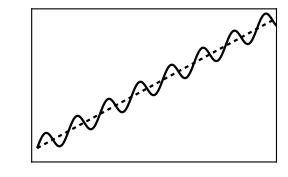

```mathematica
ClearAll[Ω,τ,Δ𝔼,acWave,dcWave];

Δ𝔼=𝒻*0.005 ;
Ω=6.4*π//N;
τ=16/2^11;

acWave=Table[((j*τ)+Δ𝔼*Sin[Ω*j*τ]),{j,0,2^11//N}];
dcWave=Table[(j*τ),{j,0,2^11//N}];
ListPlot[{acWave,dcWave},
Joined->True,
ImagePadding->{{5,5},{5,5}},
PlotStyle-> {Black,Directive[Black,Dashing[{.01,.01}]]},
Frame->True,
FrameTicks-> False,
PlotRange-> {{0,300},{-0.2,2.5}}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Plot of jτ+ΔEsin(Ωjτ) for j=0 to 2048, where Ω is the dimensionless angular frequency, τ is the dimensionless potential step size and Δ E is the sine wave amplitude. Also shown is the underlying dc sweep (------).

Using a three point approximation the surface boundary condition for linear sweep voltammetry is modified for sine wave ac voltammetry to

(3 c_1^k-4 c_2^k+c_3^k)=2 k_s^*ξ_sin^-α(ξ^(1-α)ξ_sin-c_1^k ξ^(1-α)ξ_sin-c_1^k ξ^-α)

with

ξ_sin=exp((n F)/(R T)ΔEsin(ω t))

and

k_s^*=k_s/(σD_O)^(1/2)( t/(D(n-1)))^(1/2)

The solution proceeds as described in Chapter 6. Full implementation is given in the notebook implicitACExp.nb.
Simulating the ac response requires many more time steps than when simulating a linear sweep because of the requirement that many points are needed per ac cycle to facilitate the simulation of a relatively smooth ac signal. For example it may be necessary to use 10000 to 60000 time steps. A large amount of memory can be saved by discarding all the output that isn’t needed as the simulation is taking place. Since the first three concentration points are all that is required to calculate the dimensionless current the remainder can be discarded unless you intend to simulate concentration profiles.
In the notebook implicitACExp.nb the list of concentration values for each time step is saved as a variable conc that is overwritten at each time step after the first three values are returned. 
An implicit ac method can be constructed from the linear sweep methods by redefining the value of ξ in the linear sweep methods described in Chapter 6. The code is shown below. Here an expanding grid is used in order to reduce the computation time.

ClearAll[solveACV];

solveACV[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,tmp3},

ξ=Exp[upperLimit-(τ*(k-1))-Δ𝔼*Sin[Ω*(k-1)*τ]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
tmp3=Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
(*Take[tmp3,3]*)
];

Some typical simulated ac data is contained in the file fig72.dat. This is a file containing saved graphics primitives. note

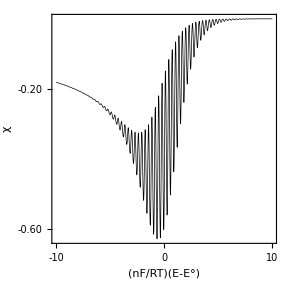

```mathematica
plot3=<<fig72.dat;
Show[plot3,FrameTicks->{ticks1[-10,10,5,5],ticks1[.2,-1.2,-.2,5],ticks2[-10,10,5,5],ticks2[.2,-1.2,-.2,5]}]
```

Fig. Chapter.FigureCaption  Simulated ac voltammogram. Implicit finite difference simulation with an expanding grid. Simulation parameters Δ E = 5  mV, Ω = 6.4 π, υ = 1  V · s^-1, k_s = 10^3 cm · s^-1, D = 2, n = 2^14, a=1.1.

The dc component can be extracted by removing the ac response with a moving average filter. The moving average takes a list, in this case the list acv1, and performs and x point moving average. To filter out the ac response we choose x to be equal to the number of increments per ac cycle. Firstly the plot points are extracted from the graphics primitives. To do this Cases is used to extract elements with the head Line since these elements are the plot points that are joined by Line in the plot. The head Line is replaced with List to give a list of plot points.

```mathematica
acv1=First[List@@First[Cases[plot3,_Line,∞]]];
```

The list acv1 contains {x,y} pairs of data. The moving average uses only the y values.

```mathematica
n=2^14;
cycles=64;

data2=MovingAverage[acv1⟦All,2⟧,Round[n/cycles]];
```

After repeating the moving average a second time a smooth linear sweep voltammogram is obtained as shown in Fig. Chapter.FigureCaption.

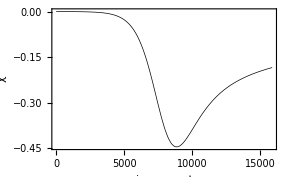

```mathematica
data2=MovingAverage[data2,Round[n/cycles]];
plot2=ListPlot[data2,optionA]
```

Fig. Chapter.FigureCaption  dc data extracted from the ac voltammogram shown in Fig. Chapter.FigureCaption extracted via a moving average filter.

The moving average reduces the length of the data list. To subtract the unfiltered data, acv1, from the filtered data, data2, the lists need to be aligned. This is done by first determining the length of the over hang.

```mathematica
ClearAll[oh];
oh=Length[acv1]-Length[data2]
```

510

Having determined the length of the overhang the overhanging points can be removed from the list of x values and the x and y lists transposed. The resulting data contain the dc voltammogram

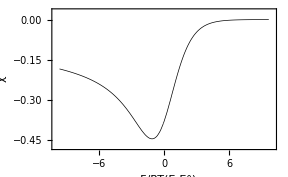

```mathematica
xpoints=Drop[Drop[acv1⟦All,1⟧,255],-255];
acv3=Transpose[{xpoints,data2}];
plot2=ListPlot[acv3,optionB,PlotRange-> {{-10,10}, {Min[data2]-0.03, Max[data2]+0.03}}]
```

Fig. Chapter.FigureCaption  A dc voltammogram extracted from the ac voltammogram shown in Fig. Chapter.FigureCaption extracted via a moving average filter.

The peak minimum is found by applying Min to the y values of the list acv3, i.e. values given by acv3⟦All,2⟧. The peak potential is found by selecting the pair of data containing the peak position. The peak height and peak position of the extracted dc voltammogram agree reasonably well with theory.

```mathematica
peakHeight=Min[acv3⟦All,2⟧];
Select[acv3,#⟦2⟧==peakHeight&]//Flatten;
Print["Peak height of ", peakHeight," positioned at ",%⟦1⟧/𝒻, " mV"]
```

Peak height of -0.444924 positioned at -0.0286374 mV

## Chapter.Section Analysis of data in the frequency domain

Each of the harmonics from an ac experiment can be isolated by first performing a Fourier transformation. In Mathematica the discrete fast Fourier transform is performed with the function Fourier and the inverse transform with InverseFourier. Best results are obtained on lists that have a length that is a power of two although Fourier will transform lists of any length. By taking the absolute value of the transformed data a power spectrum can be plotted as shown with the code below.
We want to have an x axis showing the dimensionless frequency. This can be calculated from the number of cycles. A function is written that takes each data point from the list fourierData and calls it a and returns it as a y value in an {x,y} set of data. The x value is calculated from the increment number, b, the number of cycles and the dimensionless frequency. For clarity, given that the dimensionless frequency was defined as a multiple of π, the value is stored as a multiple of π. This function is applied with the Mathematica function MapIndexed.

```mathematica
ClearAll[Ω,cycles,powerSpectrumAxis];

Ω=6.4π;
cycles=64;
powerSpectrumAxis[a_,{b_}]:={(b-1)*Ω/(cycles*Pi),a}
```

```mathematica
ClearAll[fourierData];

fourierData=Abs[Fourier[acv1⟦All,2⟧]];
fourierData=MapIndexed[powerSpectrumAxis,fourierData];
```

We now have a list of {x,y} data.

```mathematica
Short[fourierData,5]
```

{{0.,22.7512},{0.1,12.7422},{0.2,3.33614},{0.3,3.03051},{0.4,0.648057},{0.5,1.02302},«16371»,{1637.7,0.518697},{1637.8,1.02302},{1637.9,0.648057},{1638.,3.03051},{1638.1,3.33614},{1638.2,12.7422}}

The power spectrum can be plotted with an inset picture of a higher order harmonic.

```mathematica
DynamicModule[{pt=Scaled[{0.65,0.5}],data=fourierData,opt1=optionMain,opt2=optionInset},
ListPlot[data,opt1,
PlotRange->All,
Epilog->{Dynamic[Locator[Dynamic[pt],ListPlot[data,opt2,Background->None,ImageSize->150]]]}
]
]
```

Fig. Chapter.FigureCaption  Power spectrum of a simulated ac voltammogram shown in Fig. Chapter.FigureCaption after conversion to a one column format containing dimensionless current values.

The first harmonic is apparent in Fig. Chapter.FigureCaption at a dimensionless frequency of 6.4π and the second harmonic can be made out at 12.8π. The second harmonic is very small due to the small ac amplitude (5 mV) used in the simulation. The region containing the second harmonic can be expanded and shown as an inset. By isolating the first harmonic and performing the inverse Fourier transformation the first harmonic voltammogram can be obtained. Figure Chapter.FigureCaption does not show the full power spectrum. To isolate the first harmonic we set all points other than the peaks centred at 6.4π from the beginning and end of the data to zero then perform the inverse Fourier transform on this data. It is convenient to write a function to perform the isolation of particular harmonics. In the function fourierFilter two values, j and k are chosen on either side of the peak in the power spectrum that we want to isolate. This is done with the line Table[a⟦i⟧,{i,j,k}]. All other values are set to zero then the inverse transform is performed.

```mathematica
ClearAll[fourierFilter];

fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];
b=Join[Table[0.,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0.,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0.,{j,1,x-1}]];
Re[InverseFourier[b]]
];
```

After applying fourierFilter to the data the dimensionless potential corresponding to each data point is then added using MapThread. The list acv2 formed in the previous section contains this data. The dimensionless current that is plotted in Fig. Chapter.FigureCaption is dimensionless in terms of the linear sweep voltammetry scale.

π^(1/2)χ(σ t)=(i(σt))/(n F A c^* (σ D)^(1/2))

To convert it to the dimensionless scale used in ac voltammetry given in eqn (Chapter.EquationNumbered) it must be multiplied by ((R T)/(n F))1/(Δ E)(σ/ω)^(1/2).

```mathematica
ClearAll[newdata,firstHarmonic];

υ=-1.;
Δ𝔼=𝒻*0.005;
cycles=64.;
ω=Ω*𝒻*Abs[υ]; 
newdata=fourierFilter[acv1⟦All,2⟧,(Round[cycles]+1)-10,(Round[cycles]+1)+10]*Sqrt[𝒻*Abs[υ]/ω]/Δ𝔼;

(*add dimensionless potential scale to the x axis*)
firstHarmonic=MapThread[List,{acv1⟦All,1⟧,newdata}];
```

The first harmonic obtained by Fourier transformation is shown in Fig. Chapter.FigureCaption.

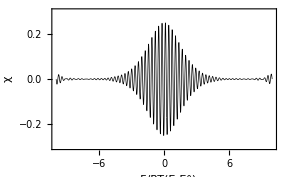

```mathematica
firstHarmonicPlot=ListPlot[firstHarmonic,optionB,PlotRange->{{-10,10},{Min[newdata]-0.05,Max[newdata]+0.05}}]
```

Fig. Chapter.FigureCaption  First harmonic extracted from the ac voltammogram shown in Fig. Chapter.FigureCaption.

The little bit of ‘ringing’ at the two edges of the plot is due to some of the dc component remaining in the filtered ac data. We can see in the power spectrum in Fig Chapter.FigureCaption that the bottom 2-3% of the first harmonic power is due to the decaying dc contribution. The procedure is repeated to obtain the second harmonic.

```mathematica
newdata2=fourierFilter[acv1⟦All,2⟧,((2*Round[cycles])+1)-11,((2*Round[cycles])+1)+11]*Sqrt[𝒻*Abs[υ]/ω]/Δ𝔼;;

(*add dimensionless potential scale to the x axis*)

secondHarmonic=MapThread[List,{acv1⟦All,1⟧,newdata2}];
```

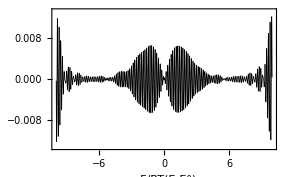

```mathematica
secondHarmonicPlot=ListPlot[secondHarmonic,optionBB,PlotRange->{{-10,10},{Min[newdata2]-0.001,Max[newdata2]+0.001}}]
```

Fig. Chapter.FigureCaption  Second harmonic extracted from the ac voltammogram shown in Fig. Chapter.FigureCaption.

The ‘ringing’ is greater in the second harmonic is due to the larger decaying dc background relative to the second harmonic compared to the first harmonic. If the ac amplitude is made larger the second harmonic is easily resolved. The file ac50.dat contains data obtained using an ac amplitude of 50 mV.

```mathematica
ClearAll[acv50];

acv50=<<acv50.dat;
```

A Fourier transform of the data is performed and the power spectrum plotted below.

```mathematica
fourierData2=Abs[Fourier[acv50]];
fourierData2=MapIndexed[powerSpectrumAxis,fourierData2];
peak2=Select[fourierData2,(#⟦1⟧==Ω/π)&];
pRange2={PlotRange:> {{1,Ceiling[5*Ω/π]},{0,Ceiling[peak2⟦1,2⟧]+1}}};
```

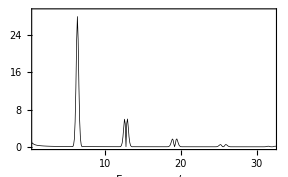

```mathematica
mainPlot=ListPlot[fourierData2,optionMain2,pRange2]
```

Fig. Chapter.FigureCaption  Power spectrum of a simulated ac voltammogram. Simulation parameters ΔE=50 mV, Ω=8π, υ=1 V · s^-1, k_s = 10^3 cm · s^-1, D=2, n=2^14.

In Fig Chapter.FigureCaption the second harmonic is well resolved. When the second harmonic is isolated from this data the resulting voltammogram is very clear.

```mathematica
newdata3=fourierFilter[acv50,((2*Round[cycles])+1)-11,((2*Round[cycles])+1)+11]*Sqrt[𝒻*Abs[υ]/ω]/Δ𝔼;
(*add dimensionless potential scale to the x axis*)
secondHarmonic2=MapThread[List,{acv1⟦All,1⟧,newdata3}];
```

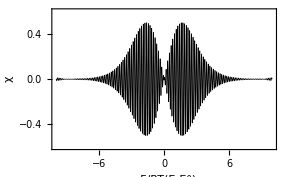

```mathematica
secondHarmonicPlot2=ListPlot[secondHarmonic2,optionB,PlotRange->{{-10,10},{Min[newdata3]-0.1,Max[newdata3]+0.1}}]
```

Fig. Chapter.FigureCaption  Second harmonic extracted from the power spectrum shown in Fig. Chapter.FigureCaption.

## Chapter.Section Square wave ac voltammetry

Chapter.Section.Subsection Square wave superimposed on a linear potential ramp

In principle the ac simulations are readily adapted to simulate a square wave superimposed on a linear potential ramp. This is done by simply noting that the sign for a sine wave alternates between plus and minus one. The square wave cycles can therefore be superimposed onto a linear ramp by substituting

ξ := Exp[(upperLimit - (j*τ) - Δ𝔼sw*Sign[Sin[Ω*j*τ]])];

In practise rounding errors occasionally cause the incorrect sign to be returned when sin(x)→ 0. A better implementation is to use the UnitStep and Mod functions. UnitStep[x] switches from zero for negative x to one for positive x. The value of x can be made to switch from negative to positive after a set number of increments using Mod.

```mathematica
tN=5;
testMod=Table[-Mod[k,2*tN]+(tN-1),{k,0,20}]
```

{4,3,2,1,0,-1,-2,-3,-4,-5,4,3,2,1,0,-1,-2,-3,-4,-5,4}

Applying UnitStep to this list we get:

```mathematica
UnitStep[testMod]
```

{1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1}

Therefore the square wave can be generated as follows:

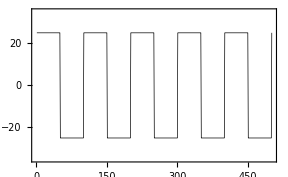

```mathematica
Clear[Δ𝔼sw,tN,τ,sw];
Δ𝔼sw=25;
tN=50;
τ=0.025;

sw=Table[(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)])),{k,0,500}];

ListPlot[sw,PlotRange-> {{0,Length[sw]},{-Δ𝔼sw-10,Δ𝔼sw+10}}]
```

Fig. 8.FigureCaption  Simulation of a square wave.

For a square wave of amplitude Δ𝔼sw containing tN steps the potential at the kth step of step size τ is described by:

ξ=Exp[upperLimit-(τ*k)-(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)]))];

Square wave voltammetry, with the square wave superimposed on a linear potential ramp is implemented in the notebook implicitSWExp1.nb.

### Chapter.Section.Subsection Square wave superimposed on a staircase potential ramp

A square wave superimposed on a staircase potential ramp is the typical implementation of the square wave method in electrochemistry. A staircase waveform can be created using the Mod function:

```mathematica
tN=5;

testMod=Table[k-Mod[k,tN],{k,0,20}]
```

{0,0,0,0,0,5,5,5,5,5,10,10,10,10,10,15,15,15,15,15,20}

Thus a staircase sweep can be simulated:

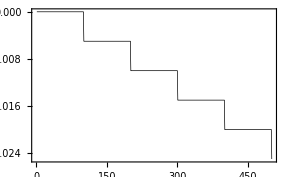

```mathematica
Clear[Δ𝔼s,tN,sw];
Δ𝔼s=.005;
tN=50;
sw=Table[-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),{k,0,500}];

sw//ListPlot
```

Fig. 8.FigureCaption  Simulation of a staircase waveform.

Adding the staircase waveform to the square wave gives the equation for the potential at the kth time increment.

ξ:=Exp[upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN)))-(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)]))]

and defining a square wave amplitude Δ E_sw, a staircase step amplitude Δ E_s, and a square wave pulse width t_p, will allow the simulation of a square wave voltammogram.

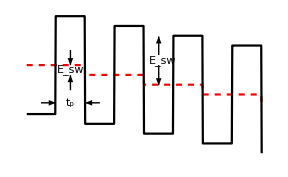

```mathematica
ClearAll[Δ𝔼s,Δ𝔼sw,tN,upperLimit,sw,sc,label1,label2];

Δ𝔼s=𝒻*0.005;
Δ𝔼sw=𝒻*0.025;
tN=64;
upperLimit=10.;

sw=Table[upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN)))-(Δ𝔼sw*2.*(-0.5+UnitStep[-Mod[k,2*tN]+(tN-1)])),{k,1,512}];

sc=Table[upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),{k,1,512}];

label1=DisplayForm[Row[{Subscript[Style["E",FontFamily-> "Times",FontSlant-> Italic],Style["sw",FontFamily-> "Times",FontSize-> 8]]}]];

label2=DisplayForm[Row[{Subscript[Style["t",FontFamily-> "Times",FontSlant-> Italic],Style["p",FontFamily-> "Times",FontSize-> 8]]}]];

ListPlot[{sc,sw},
Frame->False,
Epilog-> {
Text[label1,{296,10.1}],
Text[label1,{96,9.92}],
Text[label2,{96,9.25}],
Arrowheads[{0,.03}],
Arrow[{{288,10.},{288,9.6}}],
Arrow[{{288,10.2},{288,10.57}}],
Arrow[{{96,10.3},{96,10.}}],
Arrow[{{96,9.5},{96,9.8}}],
Arrow[{{160,9.25},{128,9.25}}],
Arrow[{{32,9.25},{64,9.25}}],
Dashing[{0.005,0.005}]},
ImageSize-> 288,
PlotRange->Full,
PlotStyle->{{Red,Dashing[{0.015,0.015}]},Black}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Square waveform as implemented by digital equipment with the underlying staircase sweep shown as a dashed line. Δ E_sw - square wave amplitude, Δ E_s - staircase step amplitude, t_p square wave pulse width.

The electrochemical literature defines a dimensionless square wave current, ψ, as

ψ=(i(t))/(n F A c_O^*)((π t_p)/D_O)^(1/2)

The simulated data can be converted to the dimensionless square wave scale used in the literature by noting that t_p equals t_n divided by twice the number of square wave cycles.

Full implementation of the square wave voltammogram is given in the notebook implicitSWExp2.nb.

The file fig715.dat contains some simulated square wave data.

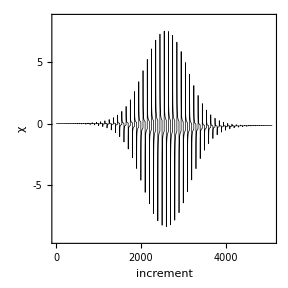

```mathematica
ClearAll[sw50];

sw50=<<fig715.dat;
Show[sw50,FrameTicks->{ticks1[0,5000,1000,5],ticks1[-10,10,5,5],ticks2[0,5000,1000,5],ticks2[-10,10,5,5]}]
```

Fig. Chapter.FigureCaption  Simulated reversible square wave voltammogram. Δ E_sw=50 mV, Δ E_s=5 mV.

```mathematica
Short[FullForm[sw50],20]
```

Graphics[\[LeftSkeleton]1\[RightSkeleton],List[Rule[PlotRange,List[List[0,5100],List[-9.33483,8.47989]]],Rule[AspectRatio,1],RuleDelayed[DisplayFunction,$DisplayFunction],Rule[ColorOutput,Automatic],Rule[Axes,False],Rule[AxesOrigin,Automatic],Rule[PlotLabel,None],Rule[AxesLabel,None],Rule[Ticks,Automatic],Rule[GridLines,None],Rule[Prolog,List[]],Rule[Epilog,List[]],Rule[AxesStyle,Automatic],Rule[Background,Automatic],Rule[DefaultColor,Automatic],RuleDelayed[DefaultFont,$DefaultFont],Rule[RotateLabel,True],Rule[Frame,True],Rule[FrameStyle,List[RGBColor[0.,0.,0.],AbsoluteThickness[0.5]]],Rule[FrameTicks,List[Automatic,yTicks2,Automatic,yTicks4]],Rule[FrameLabel,List["increment","\[Chi]",None,None]],Rule[ImageSize,List[288,288]],Rule[TextStyle,List[Rule[FontFamily,"Arial"],Rule[FontSize,10],Rule[FontWeight,"Plain"],Rule[FontColor,RGBColor[0.,0.,0.]]]],Rule[FormatType,TraditionalForm]]]

We want to recover {x,y} data points from the stored plot data. The following use of Cases would normally be satisfactory for extracting these elements.

```mathematica
Short[Cases[sw50,{_,_},∞],15]
```

{{1.,-0.00355244},{2.,-0.00212146},{3.,-0.00156783},{4.,-0.0012882},{5.,-0.00111779},{6.,-0.00100086},{7.,-0.000914349},{8.,-0.000847004},{9.,-0.000792653},{10.,-0.000747588},{11.,-0.000709433},{12.,-0.000676585},{13.,-0.000647916},{14.,-0.000622609},{15.,-0.000600055},{16.,-0.000579788},{17.,-0.000561445},{18.,-0.00054474},{19.,-0.000529443},{20.,-0.000515367},«5066»,{5087.,-0.146181},{5088.,-0.146152},{5089.,-0.146122},{5090.,-0.146092},{5091.,-0.146062},{5092.,-0.146032},{5093.,-0.146002},{5094.,-0.145971},{5095.,-0.145941},{5096.,-0.14591},{5097.,-0.145879},{5098.,-0.145848},{5099.,-0.145817},{5100.,-0.145786},{5101.,-0.150635},{0,5100},{-9.33483,8.47989},{{0,5100},{-9.33483,8.47989}},{RGBColor[0., 0., 0.],AbsoluteThickness[0.5]},{288,288}}

However the output also contains some plot options. These could be easily removed but it is better not to extract them in the first place. All the data points in a plot are in fact the arguments of a Line graphics primitive as executing FullForm[sw50] demonstrated. This next function removes only data from the stored plot information.

```mathematica
Short[Cases[sw50,Line[_],∞],15]
```

{Line[{{1.,-0.00355244},{2.,-0.00212146},{3.,-0.00156783},{4.,-0.0012882},{5.,-0.00111779},{6.,-0.00100086},{7.,-0.000914349},{8.,-0.000847004},{9.,-0.000792653},{10.,-0.000747588},{11.,-0.000709433},{12.,-0.000676585},{13.,-0.000647916},{14.,-0.000622609},{15.,-0.000600055},{16.,-0.000579788},{17.,-0.000561445},{18.,-0.00054474},{19.,-0.000529443},{20.,-0.000515367},«5061»,{5082.,-0.146325},{5083.,-0.146297},{5084.,-0.146268},{5085.,-0.146239},{5086.,-0.14621},{5087.,-0.146181},{5088.,-0.146152},{5089.,-0.146122},{5090.,-0.146092},{5091.,-0.146062},{5092.,-0.146032},{5093.,-0.146002},{5094.,-0.145971},{5095.,-0.145941},{5096.,-0.14591},{5097.,-0.145879},{5098.,-0.145848},{5099.,-0.145817},{5100.,-0.145786},{5101.,-0.150635}}]}

The output is messy and needs to be tidied up further. The fastest way to retrieve only the data points is to match anything contained within Line[{}] and return whatever is matched.

```mathematica
temp=Cases[sw50,Line[{a___}]:> a,∞];
Short[temp,15]
```

{{1.,-0.00355244},{2.,-0.00212146},{3.,-0.00156783},{4.,-0.0012882},{5.,-0.00111779},{6.,-0.00100086},{7.,-0.000914349},{8.,-0.000847004},{9.,-0.000792653},{10.,-0.000747588},{11.,-0.000709433},{12.,-0.000676585},{13.,-0.000647916},{14.,-0.000622609},{15.,-0.000600055},{16.,-0.000579788},{17.,-0.000561445},{18.,-0.00054474},{19.,-0.000529443},{20.,-0.000515367},«5061»,{5082.,-0.146325},{5083.,-0.146297},{5084.,-0.146268},{5085.,-0.146239},{5086.,-0.14621},{5087.,-0.146181},{5088.,-0.146152},{5089.,-0.146122},{5090.,-0.146092},{5091.,-0.146062},{5092.,-0.146032},{5093.,-0.146002},{5094.,-0.145971},{5095.,-0.145941},{5096.,-0.14591},{5097.,-0.145879},{5098.,-0.145848},{5099.,-0.145817},{5100.,-0.145786},{5101.,-0.150635}}

```mathematica
swv4=temp⟦All,2⟧;
```

By sampling the current at the end of the forward and reverse cycles of the square wave separate forward, χ_f, and backward, χ_b, dimensionless currents can be calculated and a voltammogram with the difference current, Δχ=χ_f-χ_b, plotted. This is the traditional way that square wave voltammograms are plotted. Figure Chapter.FigureCaption shows typical square wave voltammograms in which the current is sampled only at the end of the forward and reverse pulses.

```mathematica
ClearAll[Δ𝔼s,Δ𝔼sw,tN,Ω,cycles];

tN=50;
Δ𝔼s=2*𝒻*0.005;
Δ𝔼sw=𝒻*0.05;
Ω=16.1349;
cycles=51;
```

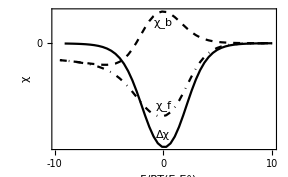

```mathematica
(*forward current*)
squareFor=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),swv4⟦k⟧},{k,tN,Length[swv4],2*tN}];
squareForPlot=ListPlot[squareFor,PlotStyle-> Directive[Black,DotDashed]];

(*backward current*)
squareBack=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,2*tN])/(2*tN))),swv4⟦k⟧},{k,2*tN,Length[swv4],2*tN}];
squareBackPlot=ListPlot[squareBack,PlotStyle->Directive[Black,Dashed]];

(*difference current*)
squareDiff=Table[{squareFor⟦j,1⟧,(squareFor⟦j,2⟧-squareBack⟦j,2⟧)},{j,1,Length[squareBack]-1}];
squarePlot=ListPlot[squareDiff,PlotStyle-> {Black}];

Show[squarePlot,squareBackPlot,squareForPlot,PlotRange->All,optionD]
```

Fig. Chapter.FigureCaption  Simulated reversible square wave voltammogram. Δ E_sw=50 mV, Δ E_s=5 mV; χ_f is the forward sweep and χ_b the backward sweep with Δχ the difference.

Find the peak from the data:

```mathematica
peakHeight=Min[squareDiff⟦All,2⟧];
Select[squareDiff,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/𝒻," mV with height ",peakHeight]
```

peak at 6.79653 mV with height -0.910578

Find the peak by interpolation:

```mathematica
int=Interpolation[squareDiff];
res=FindMinimum[int[xx],{xx,0}];
Print["peak at ",res⟦2,1,2⟧*1000/𝒻," mV with height ",res⟦1⟧]
```

peak at 1.97144 mV with height -0.914165

Because the square waveform is periodic a square wave voltammogram can also be analyzed using the Fourier transform method. The equation for a square wave of step amplitude Δ E_sw and step time width τ is given by the Fourier series approximation:

g(x)=(4Δ E_sw)/π∑_(k=1)^∞ 1/(2k-1) sin ((2k-1)  x_)

The square waveform can be plotted after truncating the infinite series.

```mathematica
squareWave[n_,τ_,t_]:=∑_(k=1)^n (1/(2*k-1)*Sin[(2π*(2*k-1)*t)/τ])
```

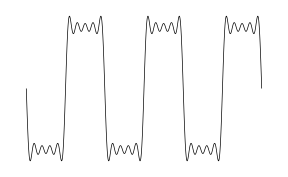

```mathematica
Plot[squareWave[5,2π,x],{x,-3π,3π},Axes-> False,Frame-> False,PlotRegion-> { {0.1,0.9},{0.1,0.9}}]
```

Fig. Chapter.FigureCaption  Plot of eqn (Chapter.EquationNumbered) for τ=2π and n=5.

As the magnitude of n in the sum is increased the plot begins to approach that expected for a square wave as shown in Fig Chapter.FigureCaption.

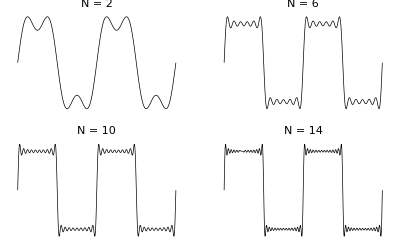

```mathematica
squareWavePlot=GraphicsGrid[
Table[Plot[Evaluate[squareWave[4*(2*i+j)-2,2π,x]],{x,-2π,2π},
Frame-> False,
BaseStyle-> {FontColor-> Black},
PlotLabel->ToString[DisplayForm[TraditionalForm[N]]]<>" = "<>ToString[4*(2*i+j)-2]],{i,0,1},{j,1,2}],
ImageSize->400]
```

Fig. Chapter.FigureCaption  Square waveforms simulated by Fourier analysis.

The Fourier transformation of the square wave voltammogram from fig. Chapter.FigureCaption is shown in Fig. Chapter.FigureCaption.

```mathematica
powerSpectrumAxis[a_,{b_}]:={(b-1)*Ω/(cycles*Pi),a}
```

```mathematica
ClearAll[fourierData3];

fourierData3=Abs[Fourier[swv4]];
fourierData3=MapIndexed[powerSpectrumAxis,fourierData3];
```

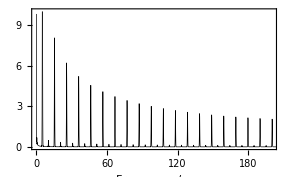

```mathematica
mainPlot=ListPlot[fourierData3,optionMain3,PlotRange->{{0,200},{0,10}}]
```

Fig. Chapter.FigureCaption  Power spectrum of the square wave voltammogram shown in Fig. Chapter.FigureCaption. The small even numbered peaks are due to the staircase waveform.

Examining the power spectrum in Fig. Chapter.FigureCaption we see that peaks occur at odd multiples of the fundamental frequency as indicated by eqn (Chapter.EquationNumbered). The successive components of the square wave still have a large amount of power due to the slow decay in the peak amplitude of the successive components of the Fourier series. The very small peaks in the power spectrum corresponding to even multiples of the fundamental frequency are due to the underlying staircase waveform. Staircase voltammetry is discussed in more detail in Chapter 8.
In principle several components from the square wave power spectrum could be isolated provided that the voltammogram has been sampled with sufficient frequency. This raises the possibility of simultaneously studying both reversible and quasi-reversible ac responses by, for example, studying the first component with an angular frequency of 100π Hz and the tenth component with an angular frequency of 1900π Hz.  note

```mathematica
Clear[𝕥,tp,υ,ω,τ];
𝕥=19.8602;
(*dimensionless potential range*)
tp=0.1;(*period in seconds*)
υ=𝕥/(𝒻*cycles*tp);(*notional sweep rate*)
ω=𝒻*.1*Ω;(*dimensional angular frequency*)
τ=𝕥/(Length[swv4]-1) ; (*calculation of the incremental time/potential step*)
```

```mathematica
ClearAll[fourierFilter];

fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];b=Join[Table[0,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0,{j,1,x-1}]];Re[InverseFourier[b]]];
```

```mathematica
Clear[newdata,firstComponent];
newdata=fourierFilter[swv4,(cycles+1)-12,(cycles+1)+12]*Sqrt[Abs[𝒻*υ]/ω]/Δ𝔼sw;

(*add dimensionless potential scale to the x axis*)
firstComponent=MapIndexed[{10.-τ*#2⟦1⟧,#1}&,newdata];
```

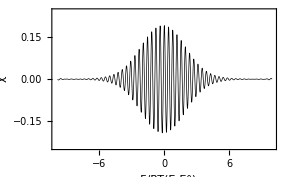

```mathematica
ListPlot[firstComponent,optionB,PlotRange->{{-10,10},{Min[newdata]-0.05,Max[newdata]+0.05}}]
```

Fig. Chapter.FigureCaption  First component of the square wave voltammogram extracted from the power spectrum shown in Fig. Chapter.FigureCaption.

The dc component can be isolated from the power spectrum in the same way as each of the ac components. The inverse Fourier transform of the dc component is shown in Fig. Chapter.15.

```mathematica
Clear[newdata4,dcComponent];
newdata4=fourierFilter[swv4,1,35];

(*add dimensionless potential scale to the x axis*)
dcComponent=MapIndexed[{10.-(τ*#2⟦1⟧),#1}&,newdata4];
```

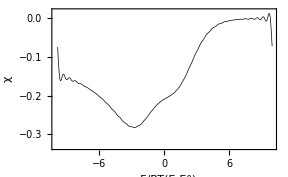

```mathematica
ListPlot[dcComponent,optionB,PlotRange->{{-10,10},{Min[newdata4]-0.05,Max[newdata4]+0.005}}]
```

Fig. Chapter.FigureCaption dc components isolated from the square wave voltammogram shown in Fig. Chapter.FigureCaption by Fourier transformation.

## Chapter.Section Summary

In this chapter we’ve shown how ac voltammograms can be simulated using Mathematica. Methods to isolate various components and harmonics from the voltammograms using discrete Fourier transforms have also been demonstrated.

## Further reading

Engblom, S. O., Myland, J. C., and Oldham, K. B. (2000). Journal of Electroanalytical Chemistry, 480, 120-132.
Gavaghan, D. J. and Bond, A. M. (2000). Journal of Electroanalytical Chemistry, 480, 133-49.
Gavaghan, D. J., Elton, D., and Bond, A. M. (2001). Journal of Electroanalytical Chemistry, 513, 73-86.
Osteryoung, J. and Odea, J. J. (1986). Square-Wave Voltammetry. In Electroanalytical Chemistry, (ed. A. J. Bard), Vol. 14. pp. 209-308, Marcel Dekker, New York.
Smith, D. E. (1966). AC polarography and Related Techniques: Theory and Practice. In Electroanalytical Chemistry, Vol. 1. (ed. A. J. Bard), pp. 1-151. Marcel Dekker, New York.
Smith, D. E. (1971). Critical Reviews in Analytical Chemistry, 2, 247-343.